```mathematica
ClearAll["Global`*"]
```

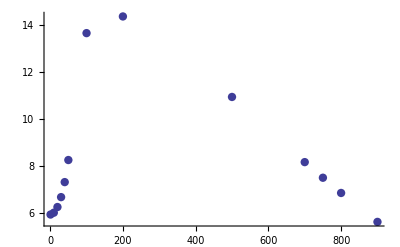

{a→0.0000279843,d→-11.7525,c→6.8049}

6.8049+(0.0000279843 (-11.7525+x)^3)/(-1+ⅇ^(1/60 (-11.7525+x)))

{a→7.38474×10^-6,c→-6.43401}

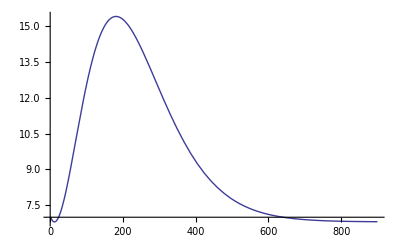

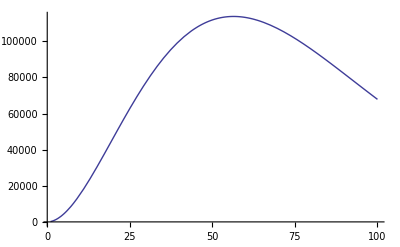

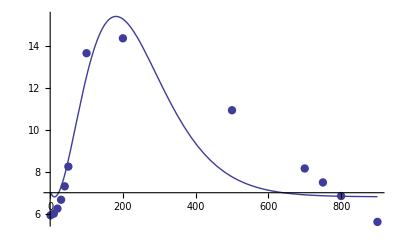

```mathematica
(*eletromagnetico 6Dz0 r+5 {k,ωi}*)
r5=ListPlot[{{1,5.9238},{10,6.0017},{20,6.2432},{30,6.6647},{40,7.3038},{50,8.2438},{100,13.6463},{200,14.3559},{500,10.9289},{700,8.1548},{750,7.48996},{800,6.84161},{900,5.61}},PlotStyle-> PointSize[0.015],PlotRange->All]
x5={{1,5.9238},{10,6.0017},{20,6.2432},{30,6.6647},{40,7.3038},{50,8.2438},{100,13.6463}};
xxx={{1,5.9238},{10,6.0017},{20,6.2432},{30,6.6647},{40,7.3038},{50,8.2438},{100,13.6463},{200,14.3559},{500,10.9289},{700,8.1548},{750,7.48996},{800,6.84161},{900,5.61}};
y=FindFit[xxx,(a (x+d)^3)/(E^((x+d) /60)-1)+c,{a,d,c},x]
yy=(a (x+d)^3)/(E^((x+ d)/60)-1) +c/.y
FindFit[x5,(a x^2)/(E^(1/x)-1)-c,{a,c},x]
rx5=Plot[yy,{x,1,900},PlotRange-> All]
Plot[(10x^3)/(E^(x /20)-1)+2,{x,1,100}]
Show[{rx5,r5},PlotRange-> All]
```

```mathematica
9
```

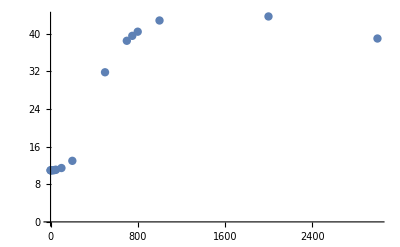

{a→0.0000833412,b→10.7715}

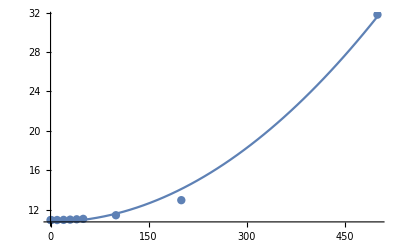

```mathematica
(*eletromagnetico 6Dz0 r+10 {k,ωi}*)
r10=ListPlot[{{0,10.9564},{1,10.9565},{10,10.9613},{20,10.9759},{30,11.0002},{40,11.0343},{50,11.0783},{100,11.4470},{200,12.9745},{500,31.7913},{700,38.4831},{750,39.5315},{800,40.4138},{1000,42.7942},{2000,43.6513},{3000,38.9648}},PlotStyle-> PointSize[0.015],PlotRange->All]
x10={{0,10.9564},{1,10.9565},{10,10.9613},{20,10.9759},{30,11.0002},{40,11.0343},{50,11.0783},{100,11.4470},{200,12.9745},{500,31.7913}};
FindFit[x10,a x^2+b,{a,b},x]
rx10=Plot[0.0000833412355120511 x^2+10.77148692098328,{x,0,500}];
Show[{rx10},r10]
```

```mathematica
(* r+5 e r+10 JUNTOS*)
ListPlot[{{{0,5.9230},{1,5.9238},{10,6.0017},{20,6.2432},{30,6.6647},{40,7.3038},{50,8.2438},{100,13.6463},{200,14.3559},{500,10.9289},{700,8.1548},{750,7.48996},{800,6.84161}},{{0,10.9564},{1,10.9565},{10,10.9613},{20,10.9759},{30,11.0002},{40,11.0343},{50,11.0783},{100,11.4470},{200,12.9745},{500,31.7913},{700,38.4831},{750,39.5315},{800,40.4138},{1000,42.7942},{2000,43.6513},{3000,38.9648}}},PlotRange->All,PlotStyle->{{Red,PointSize[0.015]},{Blue,PointSize[0.015]}},PlotRange->All,Frame-> True,FrameLabel->{"κ","ω_I"},LabelStyle->Directive[Medium],PlotLegends->Placed[ {"r_+=5","r_+=10"},{After,Center}]]
```

-Graphics-